```mathematica
{F==-(4 r^3 (r^2+1) Cos[P])/((1-r^2)^2 (1+r^2 Cos[2 P])),
Ω==((r^3+r^2)^2 Sin[2P])/((1-r^2)^2 (1+r^2 Cos[2 P])),
k==(2 (r^4+2 r^2 Cos[2 P]+1))/((1-r^2)^2 (1+r^2 Cos[2 P]))}/.{Ω->0,P->0}
```

{F==-(4 r^3)/((1-r^2)^2),True,k==(2 (1+2 r^2+r^4))/((1-r^2)^2 (1+r^2))}

```mathematica
rsol=Solve[{k==(2 (1+2 r^2+r^4))/((1-r^2)^2 (1+r^2))},r]
rsol/.k->5.
fsol=Assuming[k>0&&k∈Reals,FullSimplify[-(4 r^3)/((1-r^2)^2)/.rsol]]
```

{{r→-√(1+1/k-(√(1+4 k))/k)},{r→√(1+1/k-(√(1+4 k))/k)},{r→-√(1+1/k+(√(1+4 k))/k)},{r→√(1+1/k+(√(1+4 k))/k)}}

{{r→-0.532433},{r→0.532433},{r→-1.45482},{r→1.45482}}

{(4 √k (1+k-√(1+4 k))^(3/2))/(-1+√(1+4 k))^2,-(4 √k (1+k-√(1+4 k))^(3/2))/(-1+√(1+4 k))^2,(4 √k (1+k+√(1+4 k))^(3/2))/(1+√(1+4 k))^2,-(4 √k (1+k+√(1+4 k))^(3/2))/(1+√(1+4 k))^2}

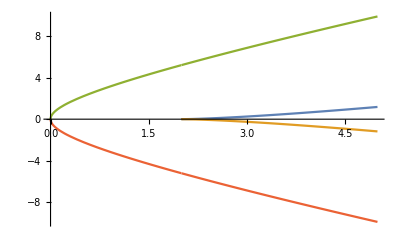

{{0.-0.300283 ⅈ},{0.+0.300283 ⅈ},{3.33019},{-3.33019}}

```mathematica
Plot[fsol,{k,0,5}]
fsol/.k->{1}//N
```

```mathematica
(*fsn=(√2 r^2 √(k^2 (r^2-1)^3+2 k (r^4-4 r^2+3)-8))/((r^2-1)^2);
Plot[fsn/.k->1,{r,0,1}]*)
```

```mathematica
fc=1/(2 k)√(((k-2) (k^4-4 k^3+4 (Ω^2+1) k^2+16 Ω^2 k+16 Ω^2))/(k+2))
fc/.k->5
fc/.k->1/.Ω->0.11406135644655635//N
```

(√(((-2+k) (-4 k^3+k^4+16 Ω^2+16 k Ω^2+4 k^2 (1+Ω^2)))/(2+k)))/(2 k)

1/10 √(3/7) √(125+96 Ω^2+100 (1+Ω^2))

0.+0.349805 ⅈ